# Planetary Motion

Filename: PlanetaryMotion_v0.18.1
Version: 0.18.1
Last Author: Jacob Snyder

## Change Log

## v0.16.1 [1-27-2016 ewn]

### Added Manipulate to visualized output. Found what appears to be logic error in math model

Reviewed v0.16 sent by JSnyder. At 10 time steps, appeared to show expected trajectories of 2 particles -- Particles moving toward each other with increasing velocity.
However, beyond 10 time steps, the particles actually passed each other, continuing on constant trajectories, still with increasing velocity.

### Proposed approach toward solution -- Inspect gravitational acceleration function

It appears gravitational acceleration function is not being updated with changing particle positions.  Particles appear to show constant acceleration based on starting positions.
IF gravitationalAccel were working properly, expect particles’ acceleration to be increasingly positive (relative to velocity) as move closer, increasingly negative (again, relative to velocity) as move away.
Rather, particles’ acceleration continues to increase (relative to velocity) as particles move away from each other -- acceleration appears to be constant.

## Description

### Heart of the Problem: Calculate gravitational interactions between 2 masses over time. Visualize the calculations

## Concepts & Terminology

## Masses exert equal, attractive force upon each other

### Newton’s Law of Universal Gravitation

forceGravity = G * mass1 * mass2 / radius^2
G = 6.67408 × 10^-11 m^3/ kg s^2

## Force changes velocity (accelerates) in proportion to mass

### Newton’s Second Law of Motion

force = mass * acceleration

## Acceleration vector {mag, dir}

### Set forceGravity = ma .. Solve for acceleration magnitude

accelGravityMagMass1 = G * mass2 / radius^2
accelGravityMagMass2 = G * mass1 / radius^2

### Acceleration direction is based on instantaneous position

Requires vector math

## Vector representation

### 2D Cartesian

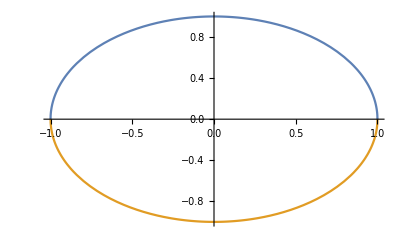

```mathematica
Plot[{√(1-x^2), -√(1-x^2)},{x,-1,1}]
```

### 2D Parametric



```mathematica
ParametricPlot[{Cos[t],Sin[t] },{t,0,2*Pi}]
```

### 2D Polar

```mathematica
PolarPlot[1,{theta,0,2 Pi}]
```

-Graphics-

## Prior Art

## Gravitational Interaction Simulator

### Code not commented, difficult to interpret

```mathematica
Manipulate[
Module[{outside,i,a,j,fg,θ},
outside=pts;
Column@{If[running,Dynamic[
For[i=1,i≤Length@pts,i++,
a={0,0};
For[j=1,j≤Length@pts,j++,
If[i≠j,
If[
Abs@(dist[pts[[i,1]],pts[[j,1]]])<radius@pts[[i,3]]+radius@pts[[j,3]],pts[[i,2]]=(pts[[i,2]]*pts[[i,3]]+pts[[j,2]]*pts[[j,3]])/(pts[[i,3]]+pts[[j,3]]);
pts[[i,1]]=(pts[[i,3]]*pts[[i,1]]+pts[[j,3]]*pts[[j,1]])/(pts[[i,3]]+pts[[j,3]]);
pts[[i,3]]=pts[[i,3]]+pts[[j,3]];pts=Delete[pts,j],
fg=(g*pts[[i,3]]*pts[[j,3]]/(dist[pts[[i,1]],pts[[j,1]]])^2)/pts[[i,3]];;
θ=ArcTan[(pts[[j,1,1]]-pts[[i,1,1]]),(pts[[j,1,2]]-pts[[i,1,2]])];
a=(a+{N@(fg*Cos[θ]),N@(fg*Sin[θ])})];
]
];
pts[[i,2]]=pts[[i,2]]+a;
pts[[i,1]]=pts[[i,1]]+pts[[i,2]];
];If[running,Text@"running",Text@"stopped"]],Text@"stopped"],EventHandler[Graphics[Dynamic[{If[dragging,{Lighter@Red,Line[{pt,MousePosition["Graphics"]}]},{}],{Darker@Hue[radius@(#[[3]])/10],Disk[#[[1]],radius@#[[3]]]}&/@pts}],PlotRange->{{0,80},{0,80}},ImageSize->{400,400}],"MouseDown":> (pt=MousePosition["Graphics"];dragging=True),"MouseUp":> (pt2=MousePosition["Graphics"];dragging=False;pts=Append[pts,{pt,(pt2-pt)/velocitydamp,10^mass}];)]}],
{{mass,2,Row[{Subscript["log",10], "(mass of planet)"}]},1,6,Appearance->"Labeled"},
{{pts,moon,"presets"},{{}->"sandbox",bigcrunch->"big crunch",galaxy->"galaxy",moon->"moon",spiral->"spiral"},PopupMenu},Row@{Button["start",running=True],Button["stop",running=False],Row@{Button["reset",pts={}]}},
{{running,False},ControlType->None},
{{dragging,False},ControlType->None},
{{pt,{0,0}},ControlType->None},
{{pt2,{0,0}},ControlType->None},
AutorunSequencing->{1},
Initialization:>(
(*Initialization Variables*)
g=0.00002;velocitydamp=100;

(*Presets*)
galaxy=(Join[{{{40,40},{0,0},10000}},Flatten[Table[Table[N@{{40,40}+n*{Cos[θ],Sin[θ]},{0,0}+{Sqrt[g*10000/n]*Cos[θ+Pi/2],Sqrt[g*10000/n]*Sin[θ+Pi/2]},10},{n,4,28,8}],{θ,0,2Pi-0.0001,Pi/4}],1]]);
spiral={{{30,40},{0,0.2},125892.54117941661},{{50,40},{0,-0.2},125892.54117941661}};
moon={{{40,40},{0,0},10^5},{{75,40},{0,Sqrt[g*10^5/35]},10^3},{{77,40},{0,Sqrt[g*10^5/35]}+{0,Sqrt[g*10^3/2]},2}};

bigcrunch={{{33.65,48.775},{0.,0.},100},{{32.35,39.074999999999996},{0.,0.},100},{{39.25,39.175},{0.,0.},100},{{29.75,41.875},{0.,0.},100},{{29.25,47.574999999999996},{0.,0.},100},{{40.25,47.875},{0.,0.},100},{{38.15,42.474999999999994},{0.,0.},100},{{33.550000000000004,44.574999999999996},{0.,0.},100},{{36.95,37.875},{0.,0.},100},{{31.55,34.574999999999996},{0.,0.},100},{{27.450000000000003,39.775},{0.,0.},100},{{25.25,46.974999999999994},{0.,0.},100},{{32.45,51.175},{0.,0.},100},{{28.150000000000002,53.275},{0.,0.},100},{{38.25,52.474999999999994},{0.,0.0010000000000000143},100},{{36.95,46.775},{0.,0.},100},{{43.95,49.074999999999996},{0.,0.},100},{{42.75,43.775},{0.,0.},100},{{39.35,45.574999999999996},{0.,0.},100},{{44.35,38.775},{0.,0.},100}};

(*Functions*)
dist[pt1_,pt2_]:=Sqrt[(pt2[[1]]-pt1[[1]])^2+(pt2[[2]]-pt1[[2]])^2];
radius[mass_]:=N@Log[10,mass]/3;
)]
```

## Planetary Orbit Model (Matlab)

http://www.mathworks.com/matlabcentral/newsreader/view_thread/301382

### Summary

Planetary orbit simulation in 3D with one sun and two
planets, all of which exert and experience gravitational forces.

Newtonian dynamics via velocity Verlet integration

Algorithm
x(t) = x(t-dt) + v(t-dt)dt + a(t-dt)/2 dt^2
a(t) = F[x(t)]/m
v(t) = v(t-dt) + [a(t) + a(t-dt)]/2 dt

Force: Gravitational towards other masses in system
F = G M m / r^2 ; F vector pointing towards other masses; r: distance

## Acceleration to Velocity

v=at

## Velocity to Displacement

x=vt

## Variable assignment

Variables can be assigned with the following syntax:
variableName = value;

## Lists

List of data, created using braces: { }

## Arrays

Data structure composed of nested lists

## Function Creation

Creation of a list of steps, created with the following syntax:
functionName[parameters] := steps/output;

## Nested Functions

Using the function NestList, functions can be applied multiple times over an initial input

## ListPlot

Plots a list of data on 2 axis

## Implementation/Pseudocode

- Create a variable containing an array containing the data of each particle
	particleAttributes = {{particleName, particleMass, {particlexPos,particleyPos}, {particlexVel,particleyVel}}, {particleName, particleMass, {particlexPos,particleyPos}, {particlexVel,particleyVel}}};
	
- Create a function that returns the gravitational acceleration between two particles, using Newton’s Law of Universal Gravitation and Newton’s Second Law (*would have to be called twice, one for each particle, where mass2 is the mass of the attracting particle*)
	gravitationalAccel[mass1, mass2, X1Pos, Y1Pos, X2Pos, Y2Pos] := {(Abs[X1Pos-X2Pos])/distanceBetween[X1Pos, Y1Pos, X2Pos, Y2Pos]) * G * mass2 * mass1 / distanceBetween[X1Pos, Y1Pos, X2Pos, Y2Pos] ^ 2, (Abs[Y1Pos - Y2Pos]) / distanceBetween[X1Pos, Y1Pos, X2Pos, Y2Pos]) * G * mass1 * mass2 / distanceBetween[X1Pos, Y1Pos, X2Pos, Y2Pos] ^ 2};
	
- Create a function that returns the distance between 2 particles
	distanceBetween[X1Pos, Y1Pos, X2Pos, Y2Pos] := Sqrt[(X1Pos-X2Pos)^2 + (Y1Pos-Y2Pos)^2];
	
- Create a function that returns the new particle velocity
	updateVelocity[initialXVel, initialYVel, mass1, mass2, X1Pos, Y1Pos, X2Pos, Y2Pos, time] := {gravitationalAccel[mass1, mass2, X1Pos, Y1Pos, X2Pos, Y2Pos][[1]]*time + initialXVel, gravitationalAccel[mass1, mass2, X1Pos, Y1Pos, X2Pos, Y2Pos][[2]]*time + initialYVel};
	
- Create a function that returns the new particle positions
	updatePosition[initialXPos, initialYPos, initialXVel, initialYVel, time] := {initialXPos + initialXVel * time, initialYPos + initialYVel * time};
	
- Create an overall particle updating function that updates the particle velocity and position by using both of the functions created previously
	updateParticles[particleAttributes] := {
		particleAttributes = ReplacePart[particleAttributes, {1,3} -> updatePosition[initialXPos, initialYPos, initialXVel, initialYVel, time]];
		particleAttributes = ReplacePart[particleAttributes, {1,4} -> updateVelocity[initialXVel, initialYVel, mass1, mass2, X1Pos, Y1Pos, X2Pos, Y2Pos, time]];
	}
	
- Use the NestList function to apply the particle updating function over several time steps
	nestedList = NestList[updateParticles, xTimes, particleAttributes]

- Use the ListPlot function to visualize the resulting array of data
	ListPlot[Map[nestedList[[#,1,3]]&, Range[xTimes]],Map[nestedList[[#,2,3]]&, Range[xTimes]]]

## Mathematica Code

```mathematica
G=6.67*10^(-11);

timeStep=1;

particle1Name="Planet A";
particle1Mass = 2500;
particle1XPos = 0;
particle1YPos = 0;
particle1XVel = 0;
particle1YVel = .04085;

particle2Name="Planet B";
particle2Mass = 25000000;
particle2XPos = 1;
particle2YPos = 0;
particle2XVel = 0;
particle2YVel = 0;

particleAttributes={{particle1Name,particle1Mass,{particle1XPos,particle1YPos},{particle1XVel,particle1YVel}},{particle2Name,particle2Mass,{particle2XPos,particle2YPos},{particle2XVel,particle2YVel}}};

gravitationalAccel[mass2_,X1Pos_,Y1Pos_,X2Pos_,Y2Pos_]:={(X2Pos-X1Pos)/distanceBetween[X1Pos,Y1Pos,X2Pos,Y2Pos]*G*mass2/(distanceBetween[X1Pos,Y1Pos,X2Pos,Y2Pos]^2),(Y2Pos-Y1Pos)/distanceBetween[X1Pos,Y1Pos,X2Pos,Y2Pos]*G*mass2/(distanceBetween[X1Pos,Y1Pos,X2Pos,Y2Pos]^2)};

distanceBetween[X1Pos_,Y1Pos_,X2Pos_,Y2Pos_]:=Sqrt[(X1Pos-X2Pos)^2+(Y1Pos-Y2Pos)^2];

updateVelocity[initialXVel_,initialYVel_,mass2_,X1Pos_,Y1Pos_,X2Pos_,Y2Pos_,time_]:={initialXVel+gravitationalAccel[mass2,X1Pos,Y1Pos,X2Pos,Y2Pos][[1]]*time,initialYVel+gravitationalAccel[mass2,X1Pos,Y1Pos,X2Pos,Y2Pos][[2]]*time};

updatePosition[initialXPos_,initialYPos_,initialXVel_,initialYVel_,time_]:={initialXPos + initialXVel*time, initialYPos + initialYVel*time};

updateParticles[particleAttributes_]:={
{particle1Name,particle1Mass,updatePosition[particleAttributes[[1,3,1]],particleAttributes[[1,3,2]],particleAttributes[[1,4,1]],particleAttributes[[1,4,2]],1],updateVelocity[particleAttributes[[1,4,1]],particleAttributes[[1,4,2]],particleAttributes[[2,2]],particleAttributes[[1,3,1]],particleAttributes[[1,3,2]],particleAttributes[[2,3,1]],particleAttributes[[2,3,2]],timeStep]},
{particle2Name,particle2Mass,updatePosition[particleAttributes[[2,3,1]],particleAttributes[[2,3,2]],particleAttributes[[2,4,1]],particleAttributes[[2,4,2]],1],updateVelocity[particleAttributes[[2,4,1]],particleAttributes[[2,4,2]],particleAttributes[[1,2]],particleAttributes[[2,3,1]],particleAttributes[[2,3,2]],particleAttributes[[1,3,1]],particleAttributes[[1,3,2]],timeStep]}
}
```

```mathematica
nested=NestList[updateParticles,particleAttributes,300]
```

{{{Planet A,2500,{0,0},{0,0.04085}},{Planet B,25000000,{1,0},{0,0}}},{{Planet A,2500,{0,0.04085},{0.0016675,0.04085}},{Planet B,25000000,{1,0},{-1.6675×10^-7,0.}}},297,{{Planet A,2500,{1.46119,1.40964},{0.0337419,-0.00873197}},{Planet B,25000000,{0.999854,0.00108045},{-3.37419×10^-6,4.9582×10^-6}}},{{Planet A,2500,{1.49493,1.40091},{0.0335057,-0.00945329}},{Planet B,25000000,{0.999851,0.00108541},{-3.35057×10^-6,5.03033×10^-6}}}}
 |  |  |  |

```mathematica
Manipulate[ListPlot[{Map[nested[[#,1,3]]&,Range[time]],Map[nested[[#,2,3]]&,Range[time]]}],{time,0,300,1, Appearance-> "Labeled"}] 
(* time changes the range is used to simulate a time series of particle movement *)
```